```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
(*Calculations for capture in White Dwarf*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20.0*10^3;(*in m/sec*)
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
clight=3 10^8(*m/sec*);
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
mn=12;(*in GeV*)
tage=3 10^17(*Age in sec*);
n=10^36(*in m^-3*);
rstar=6 10^6(*in m*);
```

```mathematica
βplus[mx_?NumericQ]:=(4 mn  mx)/(mn+mx)^2;
mr[mx_?NumericQ]:=(mn  mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626 10^-34)/(2 π);
pf=hbar (3 π^2 n)^(1/3);
kb=1.38*10^-23(*in J/k*);
```

```mathematica
rth[mx_,T_]:=((9 kb T)/(4 π G ρ mx 1.78 10^-27))^0.5;
vth[mx_,T_]:=4/3 π rth[mx,T]^3;
fMBboosted[u_]:=(3/(2 vbar^2))^(3/2)4/(√π)u^2 Exp[-3/(2 vbar^2)u^2](*Exp[-η^2] Sinh[2 (√(3/(2 vbar^2))u) η]/(2(√(3/(2 vbar^2))u) η)*) ;  
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=(vesc^2-u^2)/(vesc^2+u^2)(1+mx^2/mphi^2((u^2+vesc^2)/clight^2))/((1+mx^2/mphi^2(u/clight)^2)(1+mx^2/mphi^2(vesc/clight)^2));
y=vesc/vbar;
Cself[sigmaSelf_,mx_]:=1/3 √(6/π)ρx/mx sigmaSelf vbar(3 y^2+2Exp[-3/2 y^2]-2)
Cselfgeneral[sigmaSelf_,mx_,mphi_]:=sigmaSelf ρx/mx NIntegrate[fMBboosted[u]/u(u^2+vesc^2)(g1[u,mx,mphi]),{u,0,vesc}];
```

```mathematica
N0[mx_]:=4/3 π rstar^3 ρx/mx
```

```mathematica
tsat[sigmaSelf_?NumericQ,mx_?NumericQ,T_]:=1/Cself[sigmaSelf,mx] Log[(π (rth[mx,T])^2)/(N0[mx] sigmaSelf)]
```

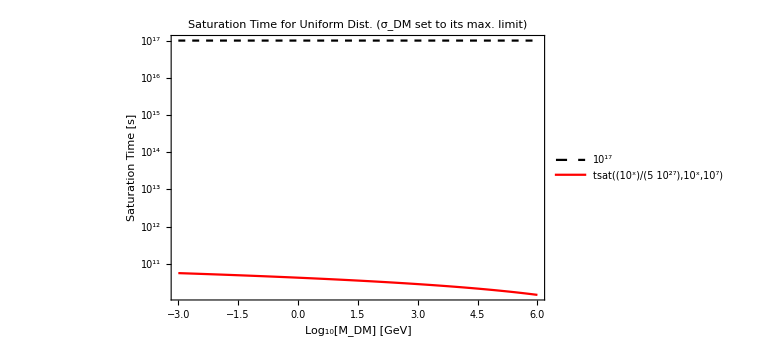

```mathematica
LogPlot[{10^17,tsat[10^x/(5 10^27),10^x,10^7]},{x,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Uniform Dist. (σ_DM set to its max. limit)"]//Quiet
```

```mathematica
tsatGen[sigmaSelf_?NumericQ,mx_?NumericQ,mphi_,T_]:=1/Cselfgeneral[sigmaSelf,mx,mphi] Log[(π (rth[mx,T])^2)/(N0[mx] sigmaSelf)]
```

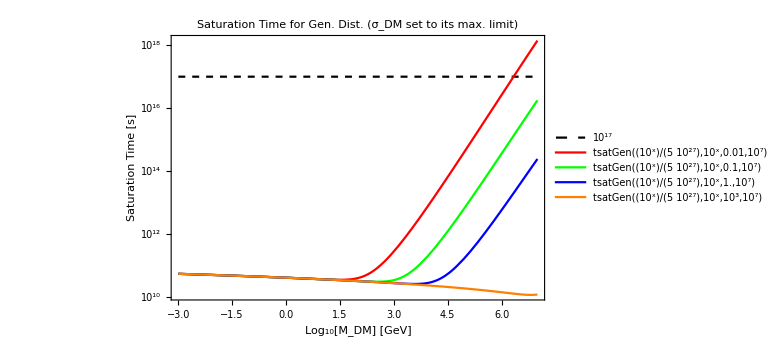

```mathematica
LogPlot[{10^17,tsatGen[10^x/(5 10^27),10^x,0.01,10^7],tsatGen[10^x/(5 10^27),10^x,0.1,10^7],tsatGen[10^x/(5 10^27),10^x,1.,10^7],tsatGen[10^x/(5 10^27),10^x,10^3,10^7]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{{Thick,Dashed,Black},Red,Green,Blue,Orange},FrameLabel->{"Log_10[M_DM] [GeV]","Saturation Time [s]"},PlotLabel->"Saturation Time for Gen. Dist. (σ_DM set to its max. limit)"]
```

```mathematica
Nfinal[sigmaSelf_?NumericQ,mx_?NumericQ,T_]:=N0[mx]Exp[Cself[sigmaSelf,mx]tsat[sigmaSelf,mx,T]]+(π rth[mx,T]^2(1/3 √(6/π)ρx/mx vbar(3 y^2+2Exp[-3/2 y^2]-2)))(tage-tsat[sigmaSelf,mx,T])
```

```mathematica
NchBoson[mx_]:=1.5 10^34(100/mx)^2(*GeV*)
NchFermion[mx_]:=1.8 10^51(100/mx)^3(*GeV*)
Nself[mx_,T_]:=4/3 π rth[mx,T]^3 ρ/mx
```

```mathematica
Nself[10^-2,10^7]
```

1.00609×10^32

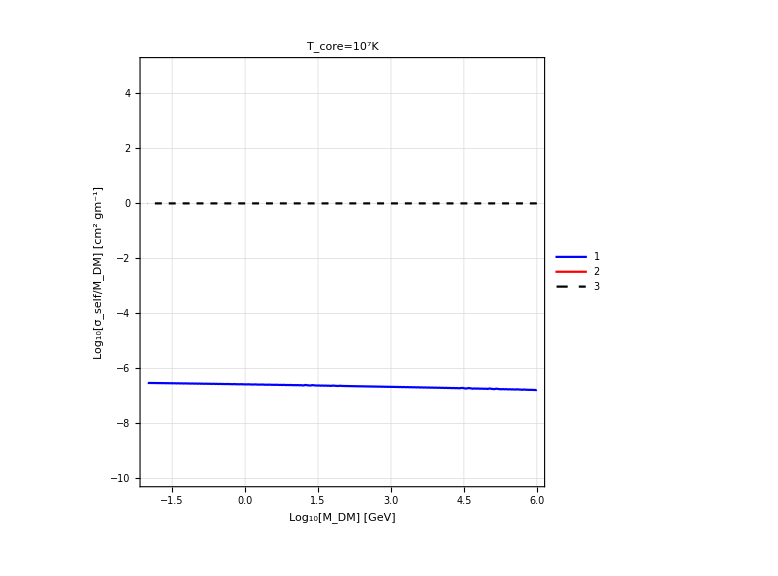

```mathematica
cntrplot1=ContourPlot[{Nfinal[(10^x)( 10^mdm)( 1.8 10^-28),10^mdm,10^7]==Max[NchBoson[10^mdm],Nself[10^mdm,10^7]],Nfinal[(10^x)( 10^mdm)( 1.8 10^-28),10^mdm,10^7]==Max[NchFermion[10^mdm],Nself[10^mdm,10^7]],x==0},{mdm,-2,6},{x,-10,5},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]//Quiet
```

```mathematica
NfinalGen[sigmaSelf_?NumericQ,mx_?NumericQ,mphi_,T_]:=N0[mx]Exp[Cselfgeneral[sigmaSelf,mx,mphi]tsatGen[sigmaSelf,mx,mphi,T]]+(π rth[mx,T]^2(ρx/mx NIntegrate[fMBboosted[u]/u(u^2+vesc^2)(g1[u,mx,mphi]),{u,0,vesc}]))(tage-tsatGen[sigmaSelf,mx,mphi,T])
```

```mathematica
NfinalGen[100/(5.62*10^27),100,10^-3,10^7]
```

1.93833×10^42

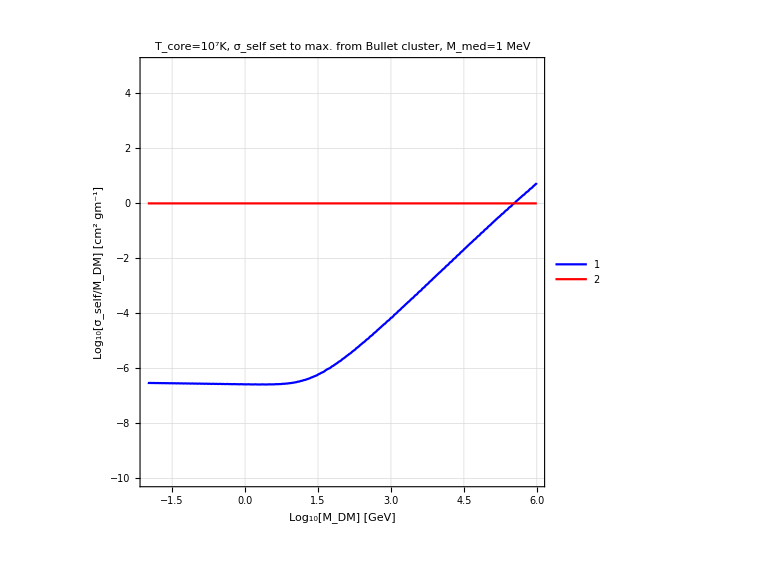

```mathematica
cntrplot2=ContourPlot[{NfinalGen[(10^x)( 10^mdm)( 1.8 10^-28),10^mdm,10^-3,10^7]==Max[NchBoson[10^mdm],Nself[10^mdm,10^7]],x==0},{mdm,-2,6},{x,-10,5},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K, σ_self set to max. from Bullet cluster, M_med=1 MeV",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]
```

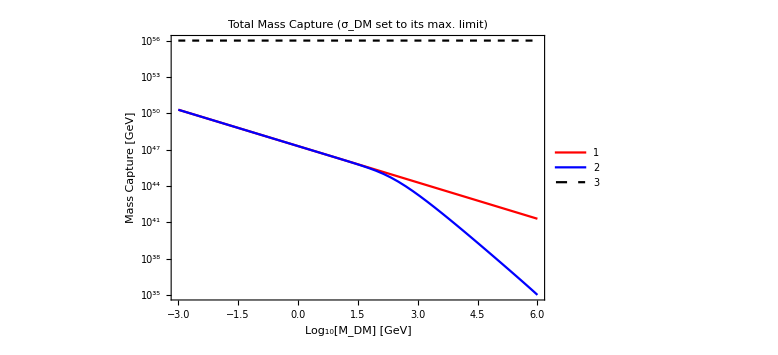

```mathematica
LogPlot[{(10^mdm )Nfinal[( 10^mdm/(5 10^27)),10^mdm,10^7],(10^mdm )NfinalGen[(10^mdm/(5 10^27)),10^mdm,0.01,10^7], 10^56},{mdm,-3,6},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->Automatic,PlotStyle->{Red,Blue,{Thick,Dashed,Black}},FrameLabel->{"Log_10[M_DM] [GeV]","Mass Capture [GeV]"},PlotLabel->"Total Mass Capture (σ_DM set to its max. limit)"]//Quiet
```

```mathematica
ttherm[mx_,sigmadmdm_,T_]:=1/(sigmadmdm*ρx/mx*((3*kb*T)/(mx*1.78*10^-27))^0.5);(*estimation of the thermalization time*)
```

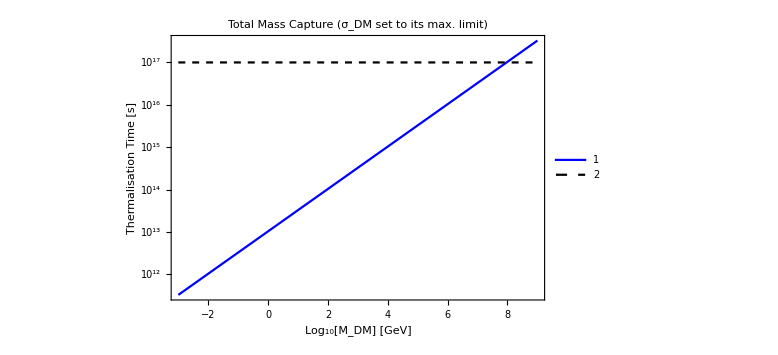

```mathematica
LogPlot[{ttherm[10^mdm,10^mdm/(5 10^27),10^7],10^17},{mdm,-3,9},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->Automatic,PlotStyle->{Blue,{Thick,Dashed,Black}},FrameLabel->{"Log_10[M_DM] [GeV]","Thermalisation Time [s]"},PlotLabel->"Total Mass Capture (σ_DM set to its max. limit)"]//Quiet
```

```mathematica
Qdiff=1.6 10^25 (ρ/(10^12(*kg/m^3*)))^(4/15)(*GeV s^-1*);
```

```mathematica
NsgEtrans[mx_,T_]:=1/5 π ρ G (4/3 π rth[mx,T]^3 ρ)rth[mx,T]^2(5.62 10^26)/clight^2
```

```mathematica
delT[mx_,sigmaSelf_,T_]:=(4/3 π rth[mx,T]^3)/(Nfinal[sigmaSelf,mx,T]sigmaSelf √(T/mx))
delTGen[mx_,mphi_,sigmaSelf_,T_]:=(4/3 π rth[mx,T]^3)/(NfinalGen[sigmaSelf,mx,mphi,T]sigmaSelf √(T/mx))
```

```mathematica
QDM[mx_,sigmaSelf_,T_]:=NsgEtrans[mx,T]/delT[mx,sigmaSelf,T]
QDMGen[mx_,mphi_,sigmaSelf_,T_]:=NsgEtrans[mx,T]/delTGen[mx,mphi,sigmaSelf,T]
```

```mathematica
(*cntrplot3=ContourPlot[{QDM[10^mdm,(10^x)( 10^mdm)( 1.8 10^-28),10^7]==Qdiff,x==0},{mdm,-2,6},{x,-10,5},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]*)
```

```mathematica
(*cntrplot4=ContourPlot[{QDMGen[10^mdm,10^-3,(10^x)( 10^mdm)( 1.8 10^-28),10^7]==Qdiff,x==0},{mdm,-2,6},{x,-10,5},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self/M_DM] [cm^2 gm^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["T_core=10^7K",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Black}}]*)
```